{0.,5.32907×10^-15,1.7053×10^-13,1.81899×10^-12,2.18279×10^-11,2.32831×10^-10,2.32831×10^-9,7.45058×10^-9,4.47035×10^-8,2.08616×10^-7,7.15256×10^-7,2.38419×10^-6,0.0000114441,0.0000228882,0.000106812,0.000244141,0.000854492,0.00244141,0.00683594,0.0214844,0.0390625,0.0625,0.1875,0.625,1.,4.,11.,30.,48.,80.,144.,256.,384.}

{0.,4.55295×10^-16,6.46234×10^-15,5.09954×10^-14,1.10024×10^-13,2.47286×10^-14,2.84763×10^-14,3.90373×10^-14,5.41333×10^-14,2.96249×10^-14,4.28295×10^-14,6.69888×10^-14,5.1472×10^-13,7.71813×10^-13,3.57142×10^-13,1.13405×10^-13,6.75299×10^-14,5.14938×10^-14,1.32587×10^-13,3.55196×10^-14,1.53133×10^-13,2.63143×10^-13,5.91795×10^-14,8.27125×10^-14,2.84039×10^-14,1.10766×10^-13,1.96238×10^-14,4.87433×10^-14,2.21036×10^-13,2.98044×10^-14,1.48962×10^-14,4.26949×10^-13,1.61973×10^-14}

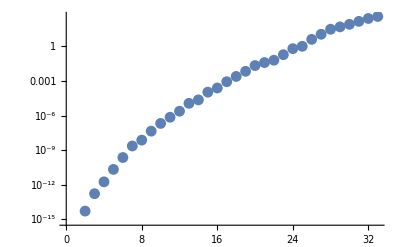

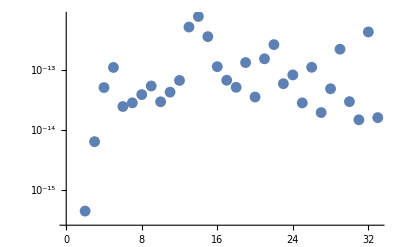

```mathematica
l = 31;
data = Import["jacobi_poly_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=JacobiP[k,-1/2,-1/2+m,y];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{0,0.,1.42109×10^-14,1.7053×10^-13,1.36424×10^-12,3.63798×10^-12,1.81899×10^-11,5.82077×10^-11,1.45519×10^-10,2.32831×10^-10,4.65661×10^-10,1.39698×10^-9,3.72529×10^-9,5.58794×10^-9,1.49012×10^-8,2.98023×10^-8,5.96046×10^-8,7.45058×10^-8,1.49012×10^-7,4.17233×10^-7,7.15256×10^-7,1.19209×10^-6,1.66893×10^-6,4.29153×10^-6,8.10623×10^-6,0.0000138283,0.0000219345,0.0000314713,0.0000476837,0.0000572205,0.0000762939,0.000087738,0.0001297}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,0.,4.30526×10^-16,2.19767×10^-15,1.13634×10^-14,1.48392×10^-14,2.89999×10^-14,2.26829×10^-13,6.30159×10^-14,2.74667×10^-14,1.58479×10^-14,7.86443×10^-14,2.16358×10^-13,1.95238×10^-14,1.84272×10^-14,5.4993×10^-14,6.80612×10^-14,1.03611×10^-13,1.39349×10^-13,5.50726×10^-14,4.0696×10^-14,1.3461×10^-13,1.32087×10^-13,7.8462×10^-14,3.55667×10^-13,3.70138×10^-13,8.81845×10^-14,7.20403×10^-13,7.23228×10^-14,4.02889×10^-14,4.47754×10^-14,4.51958×10^-14,5.425×10^-14}

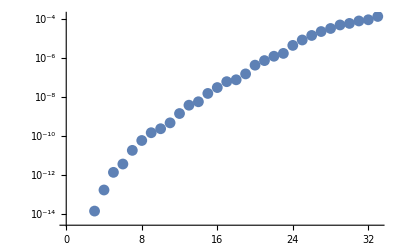

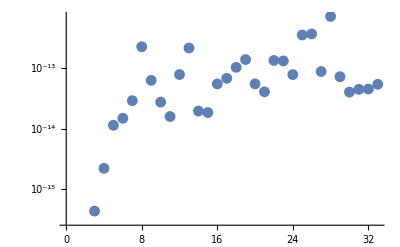

```mathematica
l = 10;
data = Import["jacobi_diff_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=If[k-1<0,0,1/2 (m+k) JacobiP[-1+k,1/2,1/2+m,y]];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{0,0,0.,1.7053×10^-13,1.81899×10^-12,1.09139×10^-11,5.82077×10^-11,2.32831×10^-10,6.98492×10^-10,2.79397×10^-9,7.45058×10^-9,1.49012×10^-8,3.72529×10^-8,1.04308×10^-7,2.68221×10^-7,4.17233×10^-7,8.34465×10^-7,1.66893×10^-6,3.8147×10^-6,9.53674×10^-6,0.0000162125,0.0000324249,0.0000457764,0.0000610352,0.00012207,0.000213623,0.000366211,0.000549316,0.0010376,0.00183105,0.00366211,0.00488281,0.00683594}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,0.,4.09003×10^-16,6.34952×10^-15,2.21807×10^-14,5.36502×10^-15,1.45121×10^-14,4.58881×10^-14,6.87154×10^-15,6.8732×10^-14,2.04508×10^-14,3.99775×10^-14,2.281×10^-14,7.07526×10^-15,1.15915×10^-14,2.11719×10^-14,4.66972×10^-14,1.25285×10^-13,1.48423×10^-13,7.0781×10^-14,7.3482×10^-14,2.92462×10^-14,6.98932×10^-13,5.63402×10^-13,1.7509×10^-13,1.03446×10^-13,3.6274×10^-14,1.54035×10^-13,1.03801×10^-13,3.56265×10^-14,4.9799×10^-14,5.04666×10^-14}

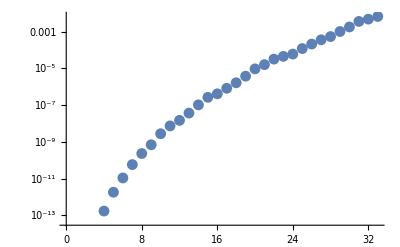

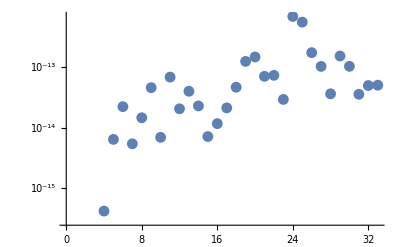

```mathematica
l = 10;
data = Import["jacobi_diff2_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=If[k-2<0,0,1/4 (k+m) (1+k+m) JacobiP[-2+k,3/2,3/2+m,y]];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{0,0,0,0.,1.36424×10^-12,2.18279×10^-11,1.16415×10^-10,1.16415×10^-9,3.72529×10^-9,1.11759×10^-8,5.96046×10^-8,1.78814×10^-7,4.76837×10^-7,1.43051×10^-6,4.29153×10^-6,0.0000104904,0.0000133514,0.0000495911,0.0000991821,0.000183105,0.000457764,0.000854492,0.00170898,0.00280762,0.00488281,0.00976563,0.0205078,0.0332031,0.0507813,0.09375,0.164063,0.25,0.40625}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,0.,5.73988×10^-16,7.28341×10^-15,5.25507×10^-15,5.43533×10^-14,2.35109×10^-14,2.0558×10^-14,1.1022×10^-14,1.16522×10^-14,5.40969×10^-13,4.36877×10^-14,7.34461×10^-14,1.53037×10^-14,1.59961×10^-14,2.86061×10^-13,8.24875×10^-14,2.72538×10^-12,2.62548×10^-14,1.85991×10^-14,1.41848×10^-12,5.39712×10^-13,1.0597×10^-14,1.31196×10^-13,5.44088×10^-14,2.21479×10^-13,3.63626×10^-13,2.04314×10^-14,2.64431×10^-13,6.66658×10^-14,7.75974×10^-13}

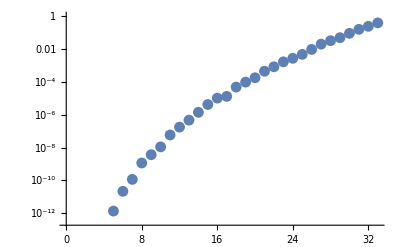

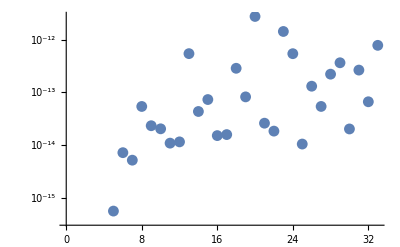

```mathematica
l = 10;
data = Import["jacobi_diff3_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=If[k-3<0,0,1/8 (k+m) (1+k+m) (2+k+m) JacobiP[-3+k,5/2,5/2+m,y]];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
check[l_,fname_,f_]:=Module[{data,x,norm,normtmp,tmp,exact,error,relError,plotValue,plotError,plotRelError},data = Import[fname<>ToString[l]<>".dat"];x = data[[;;,1]];
norm[k_]:=√Integrate[((t^l JacobiP[k,-1/2,l-1/2,2 t^2-1])^2)/(√(1-t^2)),{t,0,1}];
normtmp = Table[norm[i],{i,0,Dimensions[data][[2]]-3}];
tmp = Table[Table[f[i,l,x[[j]]]/normtmp[[i+1]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}];
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}];
Print[error];
Print[relError];
plotValue =ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All];
plotError=ListLogPlot[error];
plotRelError=ListLogPlot[relError];
Print[GraphicsGrid[{{plotValue,plotError,plotRelError}},ImageSize->1000]];
];
```

{3.10862×10^-15,1.9984×10^-15,2.44249×10^-15,2.44249×10^-15,1.9984×10^-15,2.22045×10^-15}

{3.10627×10^-15,3.06552×10^-15,2.96787×10^-15,2.70144×10^-15,1.54118×10^-14,7.49164×10^-15}

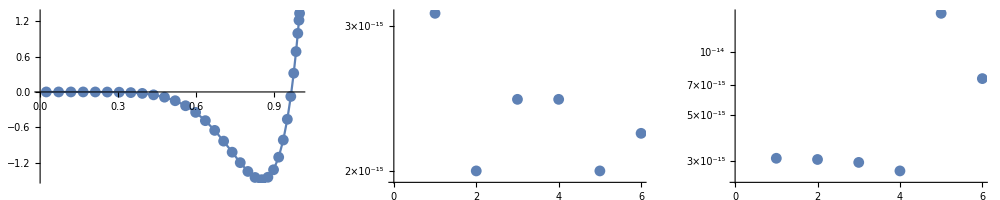

```mathematica
poly[k_,m_,y_]:=y^m JacobiP[k,-1/2,m-1/2,2 y^2-1];
check[7,"worland_poly_l",poly];
```

{2.22045×10^-15,1.9984×10^-15,3.10862×10^-15,2.88658×10^-15,3.9968×10^-15,3.9968×10^-15}

{2.77665×10^-15,2.66886×10^-15,3.72574×10^-15,2.93317×10^-15,3.27776×10^-15,6.74829×10^-15}

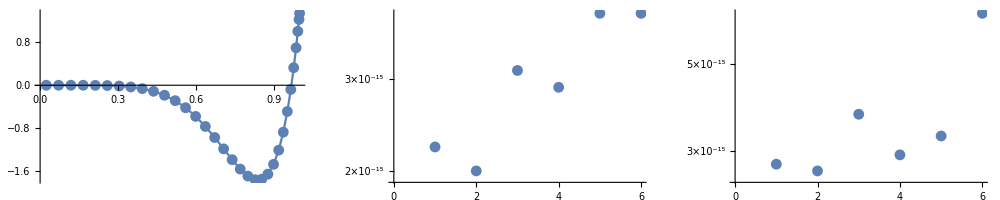

```mathematica
divr[k_,m_,y_]:=y^(m-1)JacobiP[k,-1/2,m-1/2,2 y^2-1];
check[7,"worland_divr_l",divr];
```

```mathematica
D[y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]
```

2 k y JacobiP[-1+k,1/2,1/2,-1+2 y^2]

{1.59872×10^-14,4.9738×10^-14,8.52651×10^-14,1.42109×10^-13,3.97904×10^-13,5.40012×10^-13}

{2.57832×10^-15,5.85078×10^-12,4.95981×10^-14,1.29834×10^-14,1.35681×10^-14,7.1017×10^-14}

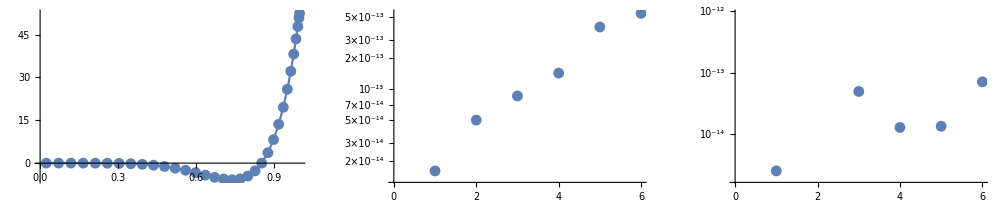

```mathematica
diff[k_,m_,y_]:=2 (k+m) y^(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+m y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2];
check[7,"worland_diff_l",diff];
```

```mathematica
D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{2.4869×10^-14,3.90799×10^-14,7.10543×10^-14,1.7053×10^-13,3.41061×10^-13,4.54747×10^-13}

{3.10627×10^-15,1.55057×10^-14,2.9489×10^-14,3.28154×10^-14,2.42018×10^-14,2.00438×10^-14}

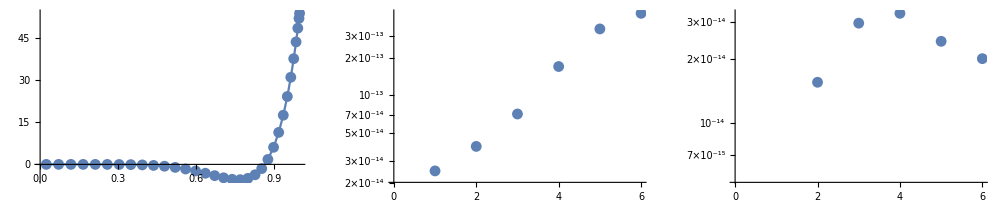

```mathematica
diffr[k_,m_,y_]:=y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]);
check[7,"worland_diffr_l",diffr];
```

```mathematica
1/y D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{1.95399×10^-14,4.26326×10^-14,8.52651×10^-14,1.98952×10^-13,3.69482×10^-13,5.11591×10^-13}

{2.77665×10^-15,1.52333×10^-14,3.15526×10^-14,3.53905×10^-14,2.11592×10^-14,2.95112×10^-14}

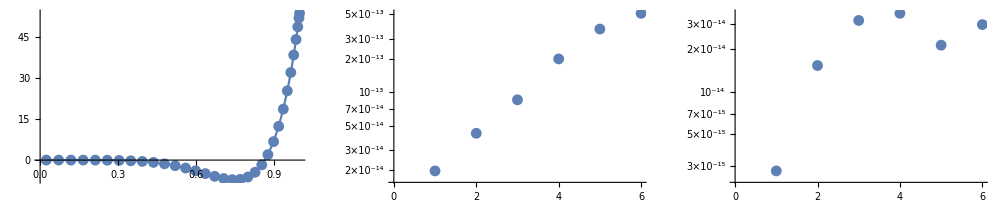

```mathematica
divrdiffr[k_,m_,y_]:=y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]);
check[7,"worland_divrdiffr_l",divrdiffr];
```

```mathematica
D[1/y D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],y]//Simplify
```

y^(-2+m) (4 (k+k^2+m+2 k m+m^2) y^4 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) (4 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]))

{0.00715363,5.68434×10^-13,9.09495×10^-13,1.81899×10^-12,1.81899×10^-12,1.09139×10^-11,1.81899×10^-11,2.91038×10^-11,3.63798×10^-11,1.01863×10^-10,1.74623×10^-10}

{1.00044,1.49867×10^-14,2.03607×10^-14,3.288×10^-14,2.11226×10^-14,2.32042×10^-14,3.8039×10^-13,1.39139×10^-14,6.11288×10^-13,1.6534×10^-14,1.26111×10^-13}

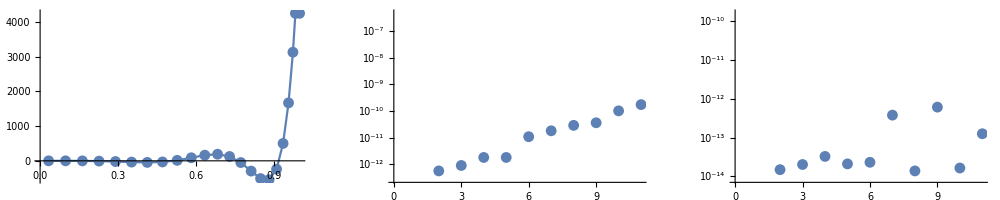

```mathematica
diffdivrdiffr[k_,m_,y_]:=y^(-2+m) (4 (k+k^2+m+2 k m+m^2) y^4 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) (4 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]));
check[7,"worland_diffdivrdiffr_l",diffdivrdiffr];
```

```mathematica
1/y^2 D[y^2 D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m(m+1)y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{0.091319,7.95808×10^-13,9.09495×10^-13,2.72848×10^-12,1.09139×10^-11,7.27596×10^-12}

{1.,3.13117×10^-15,1.01174×10^-14,1.28068×10^-14,5.02349×10^-14,4.28237×10^-14}

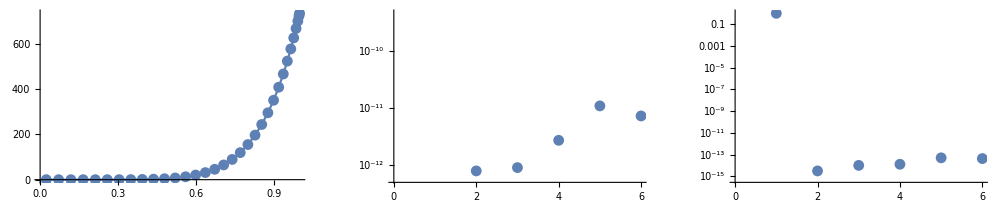

```mathematica
slapl[k_,m_,y_]:=2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[7,"worland_slapl_l",slapl];
```

```mathematica
1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{0.091319,6.82121×10^-13,9.09495×10^-13,1.81899×10^-12,7.27596×10^-12,7.27596×10^-12}

{1.,2.943×10^-15,6.41996×10^-15,1.88914×10^-14,6.8396×10^-14,1.34672×10^-12}

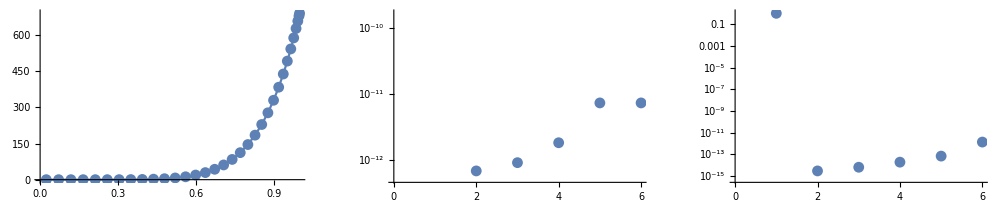

```mathematica
claplh[k_,m_,y_]:=4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[7,"worland_claplh_l",claplh];
```

```mathematica
1/y^2 D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^3//Simplify
```

4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{3.8373,7.95808×10^-13,1.36424×10^-12,1.81899×10^-12,1.09139×10^-11,1.45519×10^-11}

{1.,2.61111×10^-15,6.99475×10^-15,1.47199×10^-14,6.96207×10^-14,9.0731×10^-13}

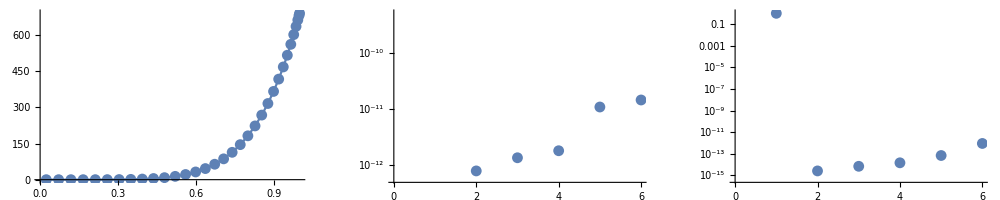

```mathematica
r1claplh[k_,m_,y_]:=4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[7,"worland_r_1claplh_l",r1claplh];
```

```mathematica
D[1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2,{y,1}]//Simplify
```

4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]+(1+k+m) (4+3 m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+m (1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{34.532,7.22223,1.45519×10^-11,8.73115×10^-11,2.32831×10^-10,2.32831×10^-10}

{1.,1.39563,3.00215×10^-14,4.09073×10^-14,1.04991×10^-13,4.14845×10^-14}

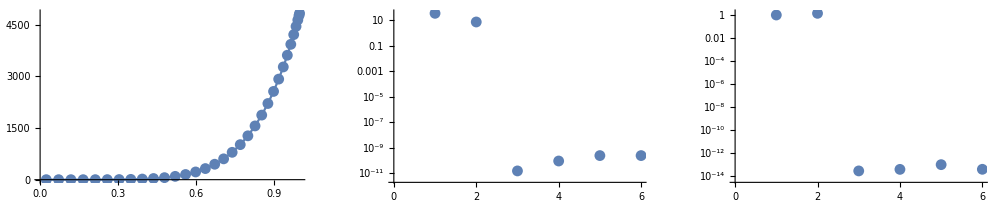

```mathematica
dclaplh[k_,m_,y_]:=4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]+(1+k+m) (4+3 m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+m (1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[7,"worland_dclaplh_l",dclaplh];
```

{2.07333,3.41271,4.2917,5.03648,5.67492,6.07672}

{0.5066,0.669017,0.725983,0.759478,0.782676,0.80012}

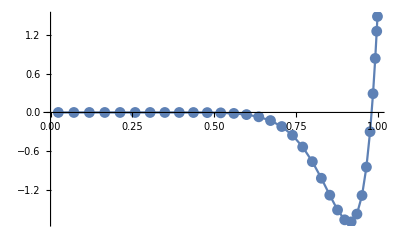

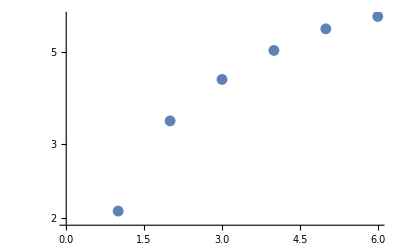

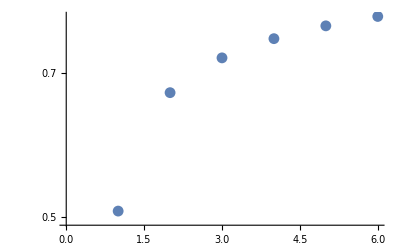

```mathematica
l = 13;
data = Import["worland_poly_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=y^m JacobiP[k,-1/2,m-1/2,2 y^2-1]/If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
norm[k_,m_]=√Integrate[((t^m JacobiP[k,-1/2,m-1/2,2 t^2-1])^2)/(√(1-t^2)),{t,0,1}];
normtmp = Table[norm[i,l],{i,0,Dimensions[data][[2]]-3}];
tmp = Table[Table[f[i,l,x[[j]]]/normtmp[[i+1]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[normtmp]
Clear[tmp]
```

```mathematica
1/y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1]
```

y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]

{2.07391,3.72229,5.20589,6.80651,8.43652,10.0529}

{0.5066,0.669017,0.725983,0.759478,0.782676,0.80012}

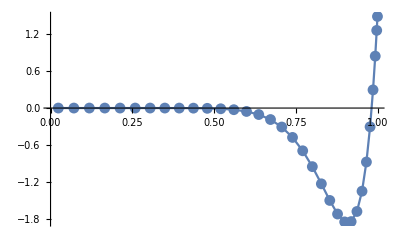

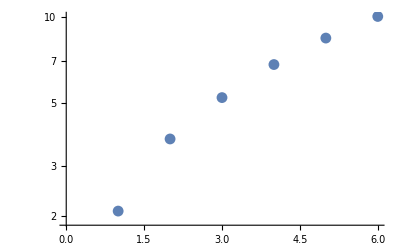

-Graphics-

```mathematica
l = 13;
data = Import["worland_divr_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]/If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
norm[k_,m_]=√Integrate[((t^m JacobiP[k,-1/2,m-1/2,2 t^2-1])^2)/(√(1-t^2)),{t,0,1}];
normtmp = Table[norm[i,l],{i,0,Dimensions[data][[2]]-3}];
tmp = Table[Table[f[i,l,x[[j]]]/normtmp[[i+1]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[normtmp]
Clear[tmp]
```

```mathematica
D[y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]
```

2 (k+m) y^(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+m y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]

{26.9609,209.252,476.14,824.807,1256.95,1774.32}

{0.5066,0.669017,0.725983,0.759478,0.782676,0.80012}

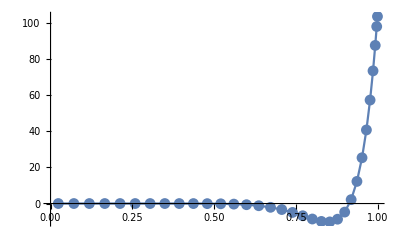

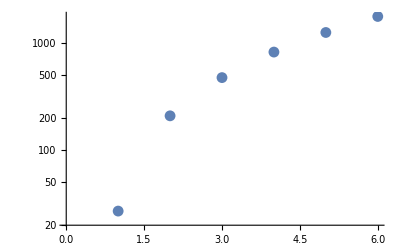

-Graphics-

```mathematica
l = 13;
data = Import["worland_diff_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=(2 (k+m) y^(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+m y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])/If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
norm[k_,m_]=√Integrate[((t^m JacobiP[k,-1/2,m-1/2,2 t^2-1])^2)/(√(1-t^2)),{t,0,1}];
normtmp = Table[norm[i,l],{i,0,Dimensions[data][[2]]-3}];
tmp = Table[Table[f[i,l,x[[j]]]/normtmp[[i+1]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[normtmp]
Clear[tmp]
```

```mathematica
D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{3.19744×10^-14,8.52651×10^-14,1.42109×10^-13,2.84217×10^-13,5.11591×10^-13,7.95808×10^-13,1.13687×10^-12,1.93268×10^-12,2.95586×10^-12,4.20641×10^-12,6.36646×10^-12,8.6402×10^-12,1.02318×10^-11,1.38698×10^-11,1.7053×10^-11,2.02363×10^-11,2.31921×10^-11,2.54659×10^-11,2.91038×10^-11,3.41061×10^-11,3.5925×10^-11,3.91083×10^-11,4.45652×10^-11,5.09317×10^-11,5.50244×10^-11,5.95719×10^-11,6.54836×10^-11,7.36691×10^-11,8.4583×10^-11,9.73159×10^-11,1.12777×10^-10,1.29148×10^-10,1.4461×10^-10}

{3.75896×10^-15,3.74976×10^-15,8.4087×10^-15,8.10541×10^-15,4.49274×10^-14,3.49806×10^-14,5.1896×10^-14,1.0537×10^-13,3.74525×10^-13,6.78825×10^-14,3.44238×10^-14,1.06157×10^-13,4.26495×10^-14,3.52094×10^-14,1.88983×10^-13,3.39252×10^-13,1.23137×10^-13,5.43043×10^-14,1.22751×10^-13,3.50844×10^-14,1.6452×10^-13,4.65946×10^-14,4.62063×10^-13,1.09243×10^-13,6.43999×10^-13,6.02516×10^-14,2.57819×10^-13,6.23143×10^-14,3.03737×10^-14,3.3886×10^-14,6.4737×10^-14,2.40571×10^-13,1.67925×10^-13}

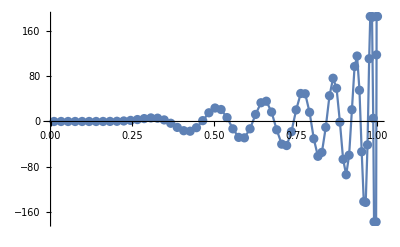

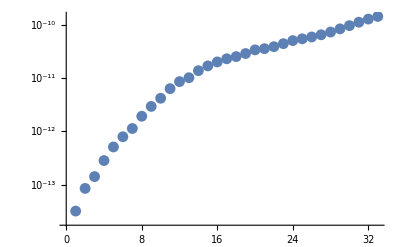

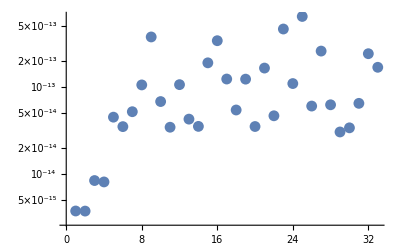

```mathematica
l = 13;
data = Import["worland_diffr_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]= y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])/If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{2.84217×10^-14,9.9476×10^-14,1.27898×10^-13,2.55795×10^-13,5.68434×10^-13,9.09495×10^-13,1.47793×10^-12,2.38742×10^-12,3.52429×10^-12,4.77485×10^-12,6.82121×10^-12,9.32232×10^-12,1.11413×10^-11,1.25056×10^-11,1.54614×10^-11,1.68257×10^-11,1.77351×10^-11,1.90994×10^-11,2.00089×10^-11,2.27374×10^-11,2.18279×10^-11,2.31921×10^-11,2.52385×10^-11,2.9786×10^-11,3.25144×10^-11,3.50155×10^-11,3.9563×10^-11,4.36557×10^-11,4.82032×10^-11,5.38876×10^-11,6.0254×10^-11,6.59384×10^-11,7.1168×10^-11}

{3.38088×10^-15,4.61402×10^-15,8.00806×10^-15,1.36546×10^-14,8.55808×10^-14,3.48968×10^-14,5.11699×10^-14,9.00536×10^-14,2.93204×10^-13,5.57956×10^-14,2.38968×10^-14,9.73226×10^-14,5.61167×10^-14,4.12466×10^-14,1.00151×10^-13,3.88665×10^-13,1.40648×10^-13,5.95816×10^-14,1.30486×10^-13,8.59414×10^-14,1.9511×10^-13,3.28958×10^-14,2.95906×10^-13,1.86895×10^-13,2.27866×10^-13,4.80232×10^-14,1.95246×10^-13,9.69399×10^-14,3.78506×10^-14,2.82634×10^-14,9.50534×10^-14,1.95893×10^-13,1.26856×10^-13}

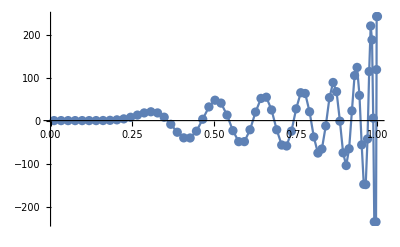

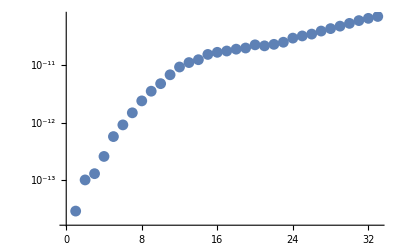

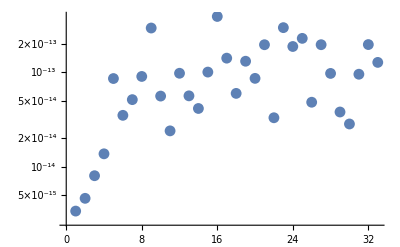

```mathematica
l = 13;
data = Import["worland_divrdiffr_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])/If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y^2 D[y^2 D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m(m+1)y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{9.70129×10^13,1.81899×10^-12,3.63798×10^-12,7.27596×10^-12,2.91038×10^-11,4.36557×10^-11,7.27596×10^-11,1.60071×10^-10,2.76486×10^-10,4.07454×10^-10,6.40284×10^-10,1.10595×10^-9,1.28057×10^-9,2.09548×10^-9,3.25963×10^-9,3.72529×10^-9,5.12227×10^-9,5.58794×10^-9,6.98492×10^-9,9.31323×10^-9,1.07102×10^-8,1.30385×10^-8,1.58325×10^-8,2.14204×10^-8,2.8871×10^-8,3.63216×10^-8,4.47035×10^-8,5.68107×10^-8,7.26432×10^-8,9.12696×10^-8,1.08033×10^-7,1.30385×10^-7,1.41561×10^-7}

{1.,3.8889×10^-15,1.7819×10^-14,6.29462×10^-15,1.76099×10^-14,1.33816×10^-14,8.84264×10^-15,6.13984×10^-14,4.25286×10^-14,2.66817×10^-14,3.19954×10^-13,6.82106×10^-14,6.74507×10^-14,1.94486×10^-14,1.6283×10^-14,8.48913×10^-14,8.03688×10^-14,9.93727×10^-14,4.38397×10^-14,2.69232×10^-14,6.52343×10^-14,9.79846×10^-14,5.07965×10^-14,4.57358×10^-14,8.8065×10^-13,3.24925×10^-14,7.61774×10^-14,9.05928×10^-14,1.38709×10^-13,4.61775×10^-14,4.16624×10^-14,6.20569×10^-14,1.53437×10^-13}

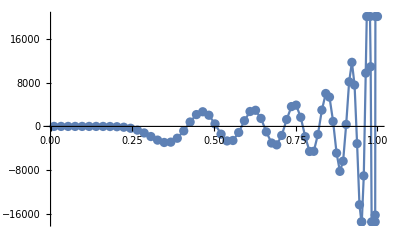

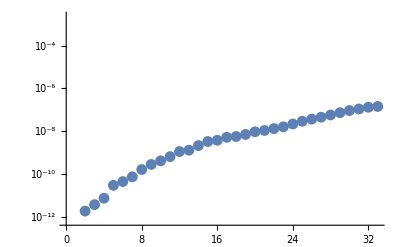

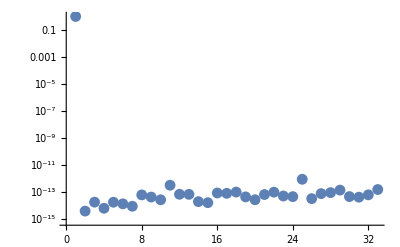

```mathematica
l = 13;
data = Import["worland_slapl_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]) /If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{9.70129×10^13,1.59162×10^-12,1.81899×10^-12,7.27596×10^-12,1.45519×10^-11,5.09317×10^-11,7.27596×10^-11,1.45519×10^-10,2.61934×10^-10,4.36557×10^-10,8.14907×10^-10,1.04774×10^-9,1.28057×10^-9,2.09548×10^-9,3.0268×10^-9,3.95812×10^-9,5.12227×10^-9,5.82077×10^-9,7.21775×10^-9,8.84756×10^-9,1.02445×10^-8,1.25729×10^-8,1.67638×10^-8,2.18861×10^-8,2.79397×10^-8,3.53903×10^-8,4.47035×10^-8,5.68107×10^-8,7.45058×10^-8,9.12696×10^-8,1.09896×10^-7,1.32248×10^-7,1.52737×10^-7}

{1.,3.83599×10^-15,7.40139×10^-15,5.27303×10^-15,2.42669×10^-14,8.29426×10^-15,7.50902×10^-15,5.05941×10^-14,1.45088×10^-13,2.87881×10^-14,5.27863×10^-14,1.94875×10^-13,3.64477×10^-14,2.71056×10^-14,1.51031×10^-14,1.2936×10^-12,4.11879×10^-14,3.60567×10^-14,6.05241×10^-14,1.62679×10^-14,2.64036×10^-14,6.87601×10^-14,5.01909×10^-14,1.69407×10^-13,1.16696×10^-12,3.67274×10^-14,2.20423×10^-14,1.2982×10^-13,3.63976×10^-13,8.64577×10^-14,3.74789×10^-14,4.1397×10^-14,3.36179×10^-13}

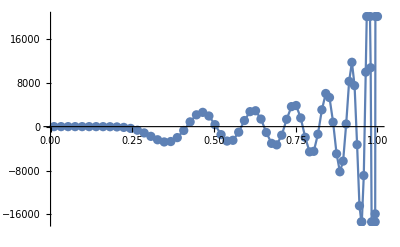

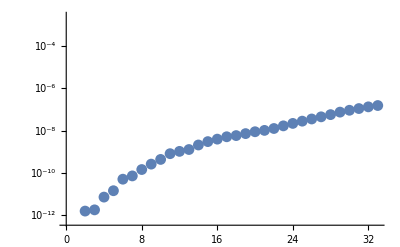

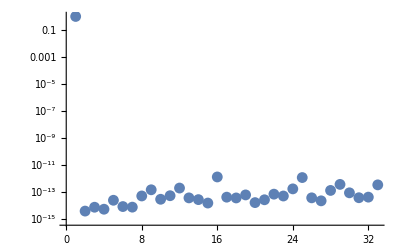

```mathematica
l = 13;
data = Import["worland_claplh_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]) /If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y^2 D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^3//Simplify
```

4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{9.01718×10^15,1.36424×10^-12,3.63798×10^-12,7.27596×10^-12,1.81899×10^-11,3.63798×10^-11,7.27596×10^-11,1.45519×10^-10,2.32831×10^-10,3.49246×10^-10,6.40284×10^-10,8.14907×10^-10,9.31323×10^-10,1.86265×10^-9,2.91038×10^-9,3.49246×10^-9,3.25963×10^-9,3.49246×10^-9,5.3551×10^-9,6.51926×10^-9,6.51926×10^-9,8.3819×10^-9,1.16415×10^-8,1.86265×10^-8,2.32831×10^-8,3.1665×10^-8,4.00469×10^-8,5.12227×10^-8,6.89179×10^-8,8.3819×10^-8,1.00583×10^-7,1.21072×10^-7,1.37836×10^-7}

{1.,3.52506×10^-15,6.63826×10^-15,6.12005×10^-15,2.90331×10^-14,9.31355×10^-15,7.83163×10^-15,2.86411×10^-14,1.60352×10^-13,1.52771×10^-14,4.64837×10^-14,2.40492×10^-13,5.61714×10^-14,5.5801×10^-14,1.97119×10^-14,8.91995×10^-13,2.67614×10^-14,4.56916×10^-14,7.01335×10^-14,2.24051×10^-14,4.09572×10^-14,5.32425×10^-14,3.61986×10^-14,9.45979×10^-14,1.28331×10^-12,3.64017×10^-14,8.08611×10^-14,1.4394×10^-13,4.77416×10^-13,7.67329×10^-14,4.10061×10^-14,4.67871×10^-14,4.66101×10^-13}

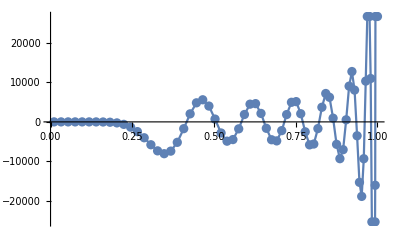

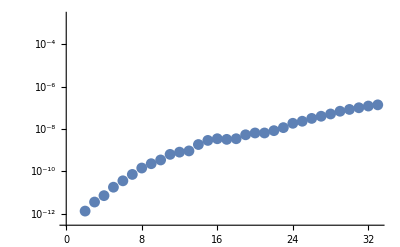

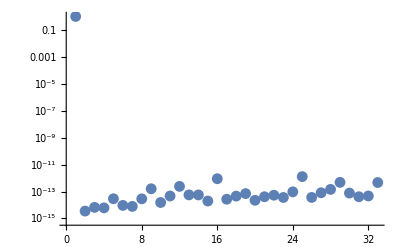

```mathematica
l = 13;
data = Import["worland_r_1claplh_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]= 4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])/If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
D[1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2,{y,1}]//Simplify
```

4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]+(1+k+m) (4+3 m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+m (1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{0.,1.81899×10^-11,1.16415×10^-10,5.82077×10^-10,1.86265×10^-9,3.25963×10^-9,6.98492×10^-9,1.30385×10^-8,1.86265×10^-8,2.98023×10^-8,7.45058×10^-8,1.19209×10^-7,1.93715×10^-7,2.08616×10^-7,2.38419×10^-7,2.68221×10^-7,2.38419×10^-7,4.17233×10^-7,9.53674×10^-7,1.19209×10^-6,1.66893×10^-6,2.5034×10^-6,3.21865×10^-6,4.29153×10^-6,4.76837×10^-6,7.15256×10^-6,0.0000109673,0.0000152588,0.0000276566,0.000043869,0.0000553131,0.0000782013,0.0000991821}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,3.08828×10^-15,1.89956×10^-14,1.47923×10^-13,7.65335×10^-14,1.45318×10^-14,3.06024×10^-14,3.89565×10^-13,1.94259×10^-13,4.02632×10^-14,2.11129×10^-14,2.01596×10^-13,1.17388×10^-13,5.443×10^-14,5.21387×10^-14,2.41845×10^-13,2.3119×10^-13,7.96985×10^-13,4.31635×10^-13,7.20638×10^-13,8.39307×10^-14,4.98823×10^-13,3.92814×10^-14,8.81784×10^-14,1.66458×10^-13,2.50077×10^-14,2.19937×10^-13,1.14378×10^-13,2.60228×10^-14,1.84696×10^-13,7.66708×10^-14,2.05546×10^-13,8.02932×10^-14}

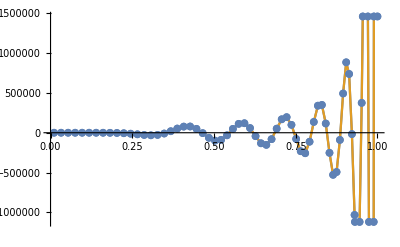

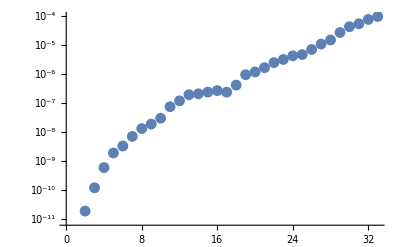

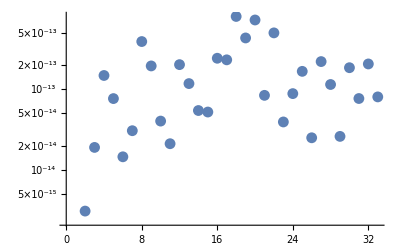

```mathematica
l = 13;
data = Import["worland_dclaplh_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]= 4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 If[k<3,0,JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]]+(1+k+m) (4+3 m) y^2 If[k<2,0, JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]]+m (1+m) If[k<1,0,JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]])/If[k==0,√(1/2(Gamma[(-1/2)+1]Gamma[m+(-1/2)+1])/Gamma[(m-1)+2]),√(1/2 1/(2k+(m-1)+1)(Gamma[k+(-1/2)+1]Gamma[k+(m-1/2)+1])/(Gamma[k+(m-1)+1]Gamma[k+1]))];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[{data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],exact[[;;,{1,Floor[Dimensions[data][[2]]/2]-1}]]},Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
endpoint[mm_,f_,col_]:=Module[{tmp,t,m,norm,data,nn},norm[n_,l_] := Table[√Integrate[((r^l JacobiP[i,-1/2,l-1/2,2 r^2-1])^2)/(√(1-r^2)),{r,0,1}],{i,0,n}];
For[m=0,m≤ mm,m++,
data = Import["cylinder_worland_endpoints_l"<>ToString[m]<>".dat"];
nn=Dimensions[data][[1]]-1;
tmp = norm[nn,m];
t=Table[f[i,1,m]/tmp[[i+1]],{i,0,nn}];
Print[Abs[N[t-data[[;;,col]],16]]];
];
];
```

```mathematica
value[n_,r_,l_]:=r^l JacobiP[n,-1/2,l-1/2,2 r^2-1]
endpoint[3,value,1];
```

{5.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17,4.6×10^-16}

{2.1×10^-16,1.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17}

{1.5×10^-16,8.×10^-17,8.×10^-17,6.×10^-17,2.5×10^-16,1.6×10^-16}

{1.3×10^-16,2.×10^-16,8.×10^-17,2.8×10^-16,6.1×10^-16,2.8×10^-16}

```mathematica
diff[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y]/.{y->r}
endpoint[3,diff,2];
```

{0.,6.×10^-17,2.×10^-16,5.×10^-15,1.×10^-15,4.9×10^-14}

{2.1×10^-16,5.×10^-16,2.1×10^-15,7.2×10^-15,6.×10^-16,3.×10^-15}

{3.×10^-16,2.4×10^-15,4.×10^-16,7.1×10^-15,2.8×10^-14,2.2×10^-14}

{6.1×10^-16,3.9×10^-15,3.1×10^-15,1.29×10^-14,7.2×10^-14,3.7×10^-14}

```mathematica
diff2[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,2}]/.{y->r}
endpoint[3,diff2,3];
```

{0.,6.×10^-17,9.4×10^-15,5.4×10^-14,4.×10^-14,1.48×10^-12}

{0.,1.4×10^-15,1.7×10^-14,1.15×10^-13,2.×10^-14,3.5×10^-13}

{3.×10^-16,6.1×10^-15,3.4×10^-14,9.×10^-14,1.01×10^-12,7.9×10^-13}

{1.23×10^-15,2.4×10^-14,2.7×10^-14,2.8×10^-13,2.65×10^-12,1.5×10^-12}

```mathematica
diff3[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,3}]/.{y->r}
endpoint[3,diff3,4];
```

{0.,0.,1.1×10^-14,7.×10^-14,1.3×10^-12,2.83×10^-11}

{0.,1.4×10^-15,7.×10^-15,8.1×10^-13,2.5×10^-12,8.×10^-12}

{0.,5.×10^-16,3.5×10^-13,2.×10^-13,1.46×10^-11,3.4×10^-11}

{1.23×10^-15,6.1×10^-14,2.1×10^-13,6.9×10^-12,6.7×10^-11,7.4×10^-11}

```mathematica
diff4[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,4}]/.{y->r}
endpoint[3,diff4,5];
```

{0.,0.,1.1×10^-14,1.9×10^-12,2.×10^-12,3.98×10^-10}

{0.,0.,1.1×10^-13,1.5×10^-12,1.6×10^-11,1.3×10^-10}

{0.,5.×10^-16,1.×10^-13,4.×10^-12,2.28×10^-10,3.9×10^-10}

{0.,2.×10^-13,2.×10^-12,5.9×10^-11,1.08×10^-9,1.92×10^-9}

```mathematica
rdiffdivr[n_,r_,l_]:=(y D[y^(l-1)JacobiP[n,-1/2,l-1/2,2 y^2-1],y])/.{y->r}
endpoint[3,rdiffdivr,6];
```

{5.×10^-17,1.8×10^-16,9.×10^-16,2.1×10^-15,5.2×10^-15,3.9×10^-14}

{0.,1.2×10^-16,1.4×10^-15,4.3×10^-15,4.8×10^-15,7.×10^-15}

{1.5×10^-16,1.2×10^-15,1.4×10^-15,1.7×10^-15,2.6×10^-14,2.2×10^-14}

{2.6×10^-16,3.7×10^-15,3.7×10^-15,8.2×10^-15,7.8×10^-14,4.7×10^-14}

```mathematica
divrdiffr[n_,r_,l_]:=(1/y D[y y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,1}])/.{y->r}
endpoint[3,divrdiffr,7];
```

{5.×10^-17,3.×10^-16,4.×10^-16,8.×10^-16,3.2×10^-15,4.4×10^-14}

{4.1×10^-16,6.×10^-16,2.7×10^-15,3.×10^-15,3.6×10^-15,1.×10^-15}

{4.5×10^-16,1.8×10^-15,7.×10^-16,1.7×10^-15,3.×10^-14,2.3×10^-14}

{5.2×10^-16,4.1×10^-15,2.5×10^-15,1.76×10^-14,6.6×10^-14,5.6×10^-14}

```mathematica
claplh[n_,r_,l_]:=(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1])/.{y->r}
endpoint[3,claplh,8];
```

{0.,1.2×10^-16,6.×10^-15,1.6×10^-14,7.×10^-15,1.4×10^-12}

{0.,5.×10^-16,4.×10^-15,2.7×10^-14,1.3×10^-13,7.×10^-14}

{0.,2.×10^-16,1.7×10^-14,6.×10^-14,6.9×10^-13,9.3×10^-13}

{0.,2.6×10^-14,7.8×10^-14,4.2×10^-13,2.92×10^-12,2.1×10^-12}

```mathematica
dclaplh[n_,r_,l_]:=D[(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1]),y]/.{y->r}
endpoint[3,dclaplh,9];
```

{0.,0.,4.×10^-15,2.7×10^-13,4.×10^-13,2.58×10^-11}

{0.,5.×10^-16,8.×10^-14,1.9×10^-13,9.×10^-13,4.×10^-12}

{0.,5.×10^-16,2.8×10^-13,1.8×10^-12,9.2×10^-12,2.5×10^-11}

{0.,7.8×10^-14,6.2×10^-13,6.1×10^-12,6.2×10^-11,9.9×10^-11}

```mathematica
clapl2h[n_,r_,l_]:=(1/y D[y D[(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1]),y],y]-l^2(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1]))/.{y->r}
endpoint[3,clapl2h,10];
```

{0.,0.,8.×10^-15,9.×10^-13,7.×10^-12,3.×10^-10}

{0.,0.,1.8×10^-13,6.×10^-12,2.6×10^-11,1.6×10^-10}

{0.,0.,3.×10^-13,1.3×10^-11,2.31×10^-10,1.07×10^-9}

{0.,0.,3.1×10^-12,6.8×10^-11,1.18×10^-9,1.67×10^-9}

```mathematica
checkStencil[start_,m_,c_]:=Module[{tmp,norm,val,ns},
ns=Dimensions[c][[1]]-1;
norm[n_,nc_,l_] := Table[1/√Integrate[((r^l JacobiP[i,-1/2,l-1/2,2 r^2-1])^2)/(√(1-r^2)),{r,0,1}],{i,n,n+nc}];
tmp = norm[start,ns,m];
val=Dot[c,norm[start,ns,m]Table[r^m JacobiP[i,-1/2,m-1/2,2 r^2-1],{i,start,start+ns}]]/.{r->1};
Print[val];
];
```

```mathematica
checkStencil[0,2,{1,-1.11803399}]
```

-1.45685×10^-9

```mathematica
√(1/4(Gamma[n+1/2]/Gamma[n+1])^2)/.{n->0}
```

(√π)/2

```mathematica
Limit[√(1/2 1/(2n-1/2+m-1/2+1)(Gamma[n+1/2]Gamma[n+m+1/2])/(Gamma[n+m]Gamma[n+1]))/.{m->0},n->0]
```

(√π)/2